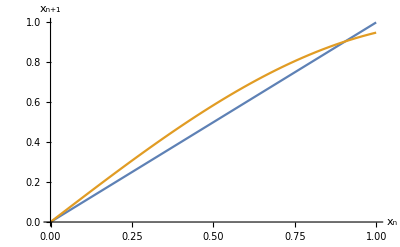

```mathematica
Plot[{x,Sin[5*x/4]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

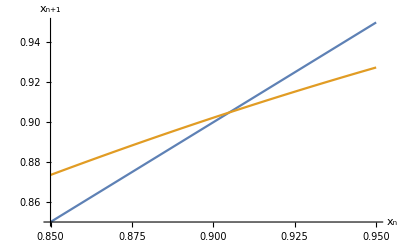

```mathematica
Plot[{x,Sin[5*x/4]},{x,0.85,0.95},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
r1=FindRoot[x==Sin[5*x/4],{x,1}]
```

{x→0.904882}

```mathematica
l1=D[Sin[5*x/4],x]/.r1
```

0.532078

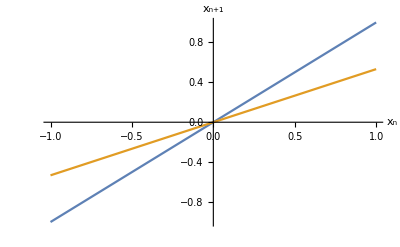

```mathematica
Plot[{x,l1*x},{x,-1,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

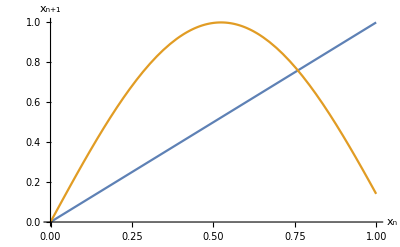

```mathematica
Plot[{x,Sin[3*x]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
Plot[{x,Sin[3*x]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
r2=FindRoot[x==Sin[3*x],{x,0.8}]
```

{x→0.759621}

```mathematica
l2=D[Sin[3*x],x]/.r2
```

-1.9511

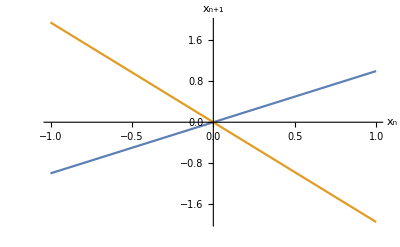

```mathematica
Plot[{x,l2*x},{x,-1,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

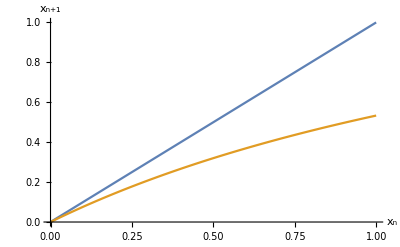

```mathematica
Plot[{x,0.8*x/(1+0.5*x)},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
sbvex=RecurrenceTable[{x[n+1]==0.8*x[n]/(1+0.5*x[n]),x[1]==1},x,{n,1,20}];
```

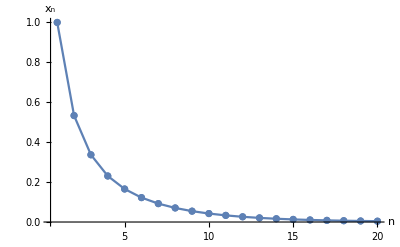

```mathematica
ListPlot[sbvex,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->Full,PlotRange->All]
```

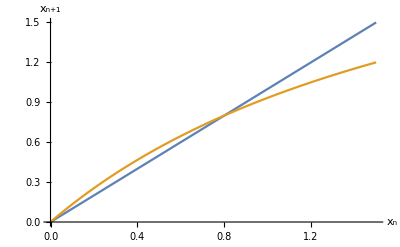

```mathematica
Plot[{x,1.4*x/(1+0.5*x)},{x,0,1.5},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
sbvsu=RecurrenceTable[{x[n+1]==1.4*x[n]/(1+0.5*x[n]),x[1]==0.01},x,{n,1,30}];
```

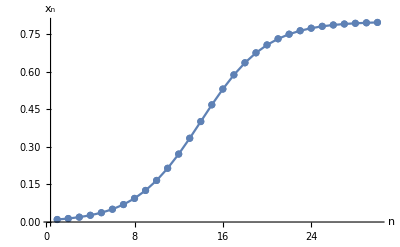

```mathematica
ListPlot[sbvsu,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->Full,PlotRange->All]
```

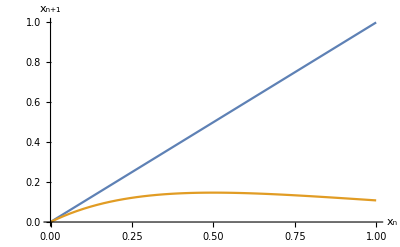

```mathematica
Plot[{x,0.8*x*Exp[-2*x]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
sriex=RecurrenceTable[{x[n+1]==0.8*x[n]*Exp[-2*x[n]],x[1]==1},x,{n,1,10}];
```

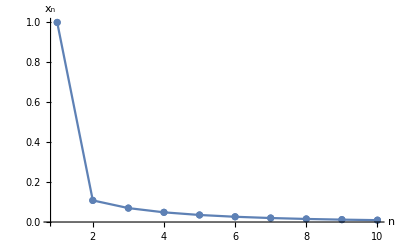

```mathematica
ListPlot[sriex,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->Full,PlotRange->All]
```

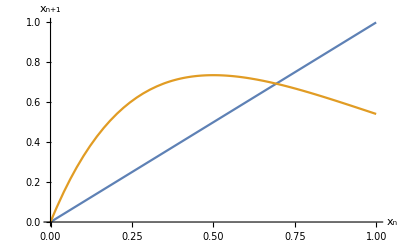

```mathematica
Plot[{x,4*x*Exp[-2*x]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
srisu=RecurrenceTable[{x[n+1]==4*x[n]*Exp[-2*x[n]],x[1]==0.01},x,{n,1,15}];
```

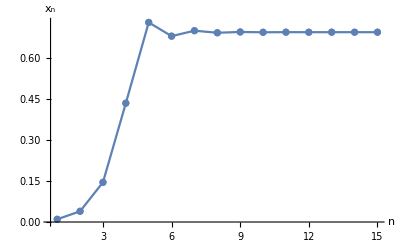

```mathematica
ListPlot[srisu,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->Full,PlotRange->All]
```

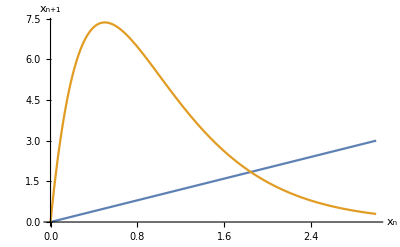

```mathematica
Plot[{x,40*x*Exp[-2*x]},{x,0,3},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
srios=RecurrenceTable[{x[n+1]==40*x[n]*Exp[-2*x[n]],x[1]==0.01},x,{n,1,50}];
```

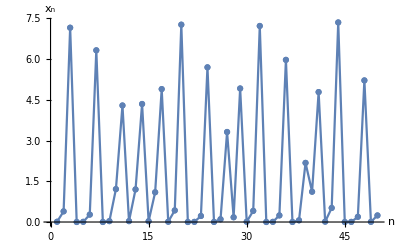

```mathematica
ListPlot[srios,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->Full,PlotRange->All]
```

```mathematica
Manipulate[Plot[{x,40*x/((1+(2/g)*x)^g)},{x,0,22},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}],{g,1,5}]
```